### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = .9;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[1-j16]&&NonNegative[j16]&&NonNegative[1-j16]&&NonNegative[j16]&&NonNegative[1-jt29]&&NonNegative[jt29]&&NonNegative[-j16+jt29]&&NonNegative[j16-jt29]&&NonNegative[j16-jt29]&&NonNegative[-j16+jt29]&&NonNegative[1-j16]&&NonNegative[j16]&&NonNegative[4-u38+u39]&&NonNegative[4-u38+u40]&&NonNegative[2+u38-u39]&&NonNegative[3-u39+u40]&&NonNegative[-1+u38-u40]&&NonNegative[u39-u40]&&NonNegative[1-j16-u39]&&NonNegative[1+j16-u40]&&(1-jt29==0||-j16+jt29==0)&&(jt29==0||j16-jt29==0)&&(j16-jt29==0||-j16+jt29==0)&&(1-jt29==0||4-u38+u39==0)&&(jt29==0||4-u38+u40==0)&&(-j16+jt29==0||2+u38-u39==0)&&(j16-jt29==0||3-u39+u40==0)&&(j16-jt29==0||-1+u38-u40==0)&&(-j16+jt29==0||u39-u40==0)&&(1-j16==0||1-j16-u39==0)&&(j16==0||1+j16-u40==0)
and the rules are:
<|j14→1,j15→1-j16,j17→1-j16,j18→j16,j19→1,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt28→1-jt29,jt30→-j16+jt29,jt31→j16-jt29,jt32→j16-jt29,jt33→-j16+jt29,jt34→1-j16,jt35→0,jt36→j16,jt37→0,u41→0,u42→1,u44→-1+u38,u45→-1+j16+u39,u46→-j16+u40,u47→0,u48→1,u49→u38,u43→u38|>

DataToEquations: It took 0.047981 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j16==0&&jt29==0&&u38==5&&u39==1&&u40==1
and the rules are:
<|j14→1,j15→1-j16,j17→1-j16,j18→j16,j19→1,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt28→1-jt29,jt30→-j16+jt29,jt31→j16-jt29,jt32→j16-jt29,jt33→-j16+jt29,jt34→1-j16,jt35→0,jt36→j16,jt37→0,u41→0,u42→1,u44→-1+u38,u45→-1+j16+u39,u46→-j16+u40,u47→0,u48→1,u49→u38,u43→u38|>

DataToEquations: Critical congestion solved.

all ok? up to here?

{j14-j20+IntM[j14-j20,1->2],j15-j21+IntM[j15-j21,2->3],j16-j22+IntM[j16-j22,2->4]}

DataToEquations: Done.

{0.079141,Null}

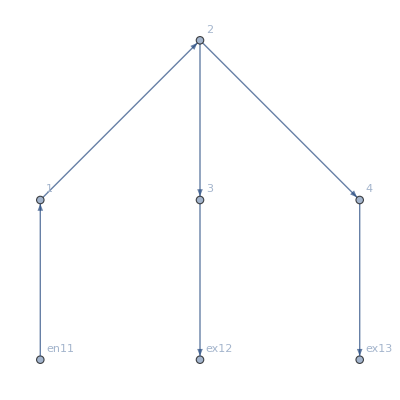

current: <|{1,1->2}→0,{1,en11->1}→1,{2,1->2}→1,{2,2->3}→0,{2,2->4}→0,{3,2->3}→1,{3,3->ex12}→0,{4,2->4}→0,{4,4->ex13}→0,{en11,en11->1}→0,{ex12,3->ex12}→1,{ex13,4->ex13}→0|>

transition: <|{1,1->2,en11->1}→0,{1,en11->1,1->2}→1,{2,1->2,2->3}→1,{2,1->2,2->4}→0,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,2->3,3->ex12}→1,{3,3->ex12,2->3}→0,{4,2->4,4->ex13}→0,{4,4->ex13,2->4}→0|>

value: <|{1,1->2}→5,{1,en11->1}→5,{2,1->2}→4,{2,2->3}→1,{2,2->4}→1,{3,2->3}→0,{3,3->ex12}→0,{4,2->4}→1,{4,4->ex13}→1,{en11,en11->1}→5,{ex12,3->ex12}→0,{ex13,4->ex13}→1|>

```mathematica
Data=DataG[t];
(MFGEquations=DataToEquations[Data/.{I1->1,U1->(*at vertex 3*)0,U2->(*at vertex 4*)1(*, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1*),S1->(*S124*)3,S2->(*S123*)3,S3->3,S4->3,S5->0,S6->0}];)//Timing
If[MFGEquations =!= Null,
Print[MFGEquations["FG"]];
Print["current: ", MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort];
Print["transition: ", MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort];
Print["value: ", MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
]
```

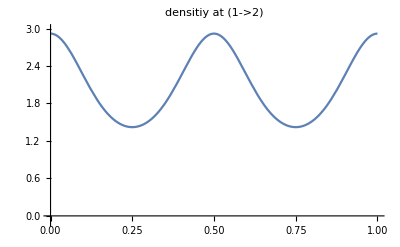
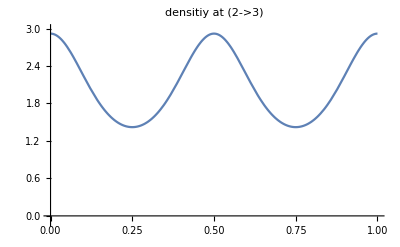
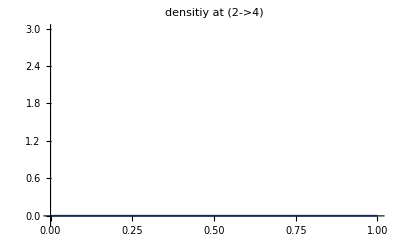

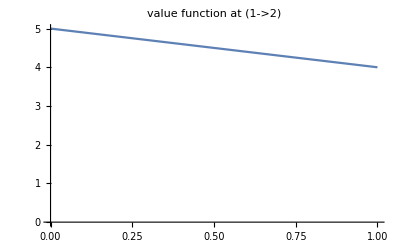
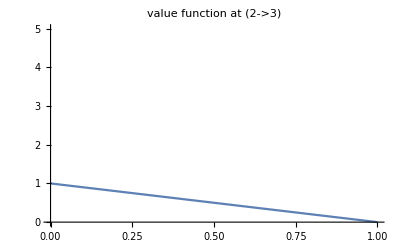
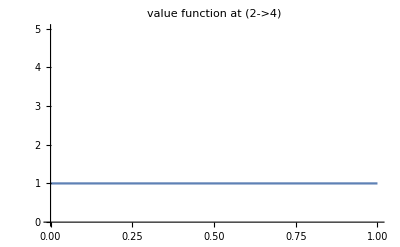

```mathematica
alpha = 1;
(*FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort*)
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"densitiy at "#, PlotRange->{-0.1,3}]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at "#, PlotRange-> {0,5}]&/@MFGEquations["BEL"]
```

#### Non-linear case

```mathematica
alpha = .1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j14-j20-u38+u44==0.414128&&j15-j21-u39+u45==0.414128&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j14-j20-u38+u44==0.414128&&j15-j21-u39+u45==0.414128&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j14→1,j15→1.,j16→0.,j17→1.,j18→0.,j19→1,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt28→1.,jt29→0.,jt30→0,jt31→0,jt32→0,jt33→0,jt34→1.,jt35→0,jt36→0.,jt37→0,u38→4.17174,u39→0.585872,u40→0.585872,u41→0,u42→1,u43→4.17174,u44→3.58587,u45→0.,u46→0.585872,u47→0,u48→1,u49→4.17174|>

### New idea: U depends on the association from DataToEquations, together with the result of some nonlinear case

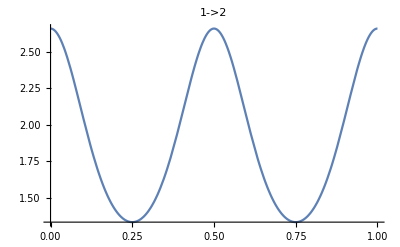
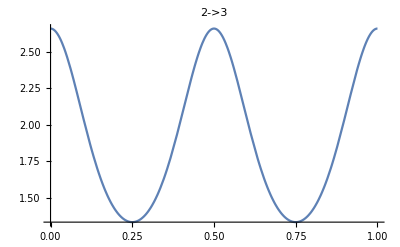
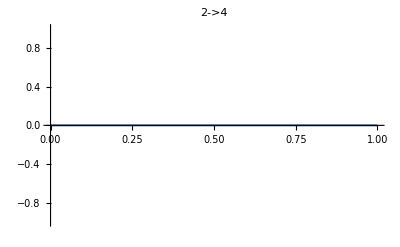

```mathematica
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```

We need to fix what happens when the current is zero... think of what the U should be! It should retain the value at the Tail of the Edge.

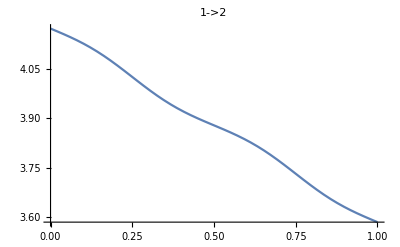
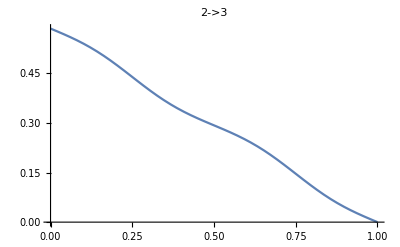
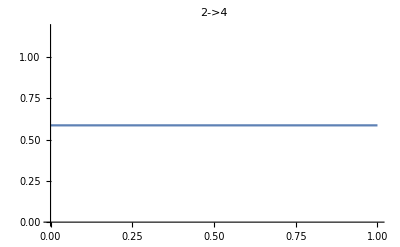

```mathematica
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```

### Comparison between U and the linear function: U is not linear, if alpha =!=1 !

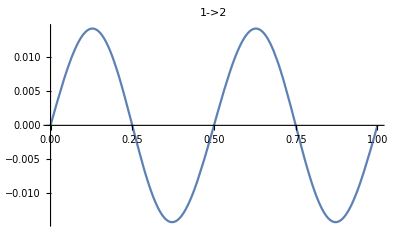
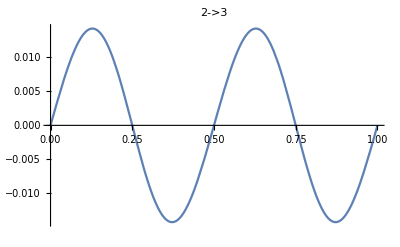
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
coeff = AssociationThread[MFGEquations["BEL"],(U[1,#,MFGEquations/.FFR]-U[0,#,MFGEquations/.FFR])&/@MFGEquations["BEL"]];
start = AssociationThread[MFGEquations["BEL"],(U[0,#,MFGEquations/.FFR])&/@MFGEquations["BEL"]];
Plot[U[x, #, MFGEquations/.FFR]-(start[#]+x*coeff[#]),{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```

FRX1: nonlinear: 
j14-j20-u38+u44==0.442779&&j15-j21-u39+u45==0.442779&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j14-j20-u38+u44==0.442779&&j15-j21-u39+u45==0.442779&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j14→1,j15→1.,j16→0.,j17→1.,j18→0.,j19→1,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt28→1.,jt29→0.,jt30→0,jt31→0,jt32→0,jt33→0,jt34→1.,jt35→0,jt36→0.,jt37→0,u38→4.11444,u39→0.557221,u40→0.557221,u41→0,u42→1,u43→4.11444,u44→3.55722,u45→0.,u46→0.557221,u47→0,u48→1,u49→4.11444|>

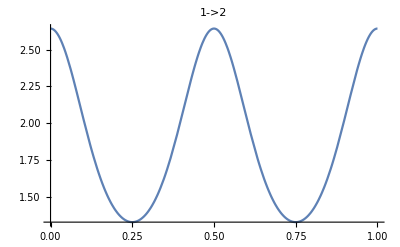
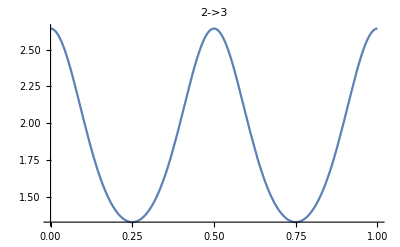
{-Graphics-,-Graphics-,-Graphics-}

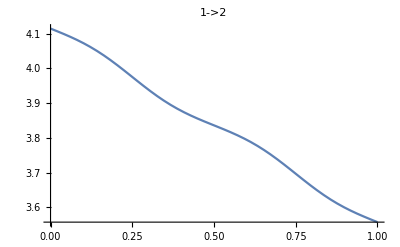
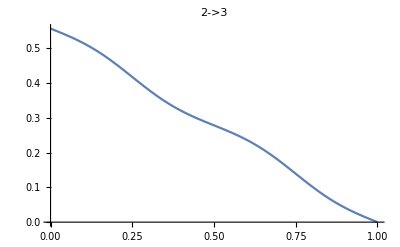
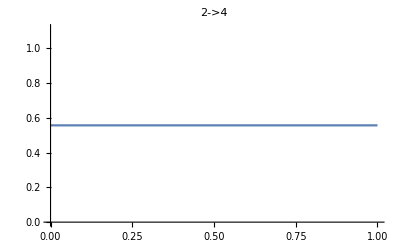

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-1.71828&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-0.0936949&&j16-j22-u40+u46==-1.18962

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-1.71828&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-0.0936949&&j16-j22-u40+u46==-1.18962

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-1.71828&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-0.0936949&&j16-j22-u40+u46==-1.18962

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-1.71828&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-0.0936949&&j16-j22-u40+u46==-1.18962

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-1.71828&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-0.0936949&&j16-j22-u40+u46==-1.18962

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

<|j14→1,j15→1.,j16→0.,j17→1.,j18→0.,j19→1,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt28→1.,jt29→0.,jt30→0,jt31→0,jt32→0,jt33→0,jt34→1.,jt35→0,jt36→0.,jt37→0,u38→6.81197,u39→1.09369,u40→1.09369,u41→0,u42→1,u43→6.81197,u44→4.09369,u45→0.,u46→-0.0959228,u47→0,u48→1,u49→6.81197|>

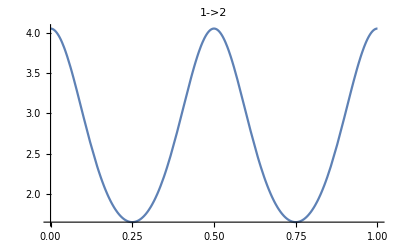
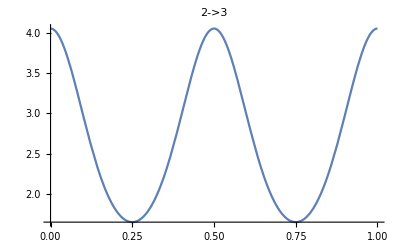
{-Graphics-,-Graphics-,-Graphics-}

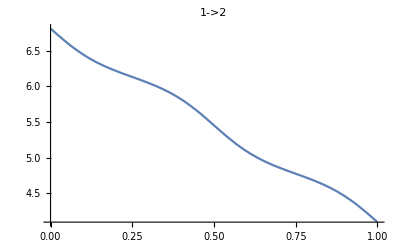
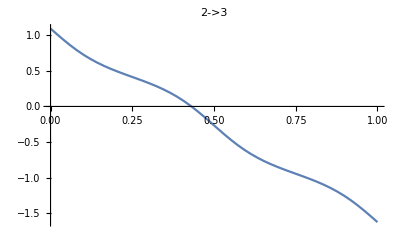
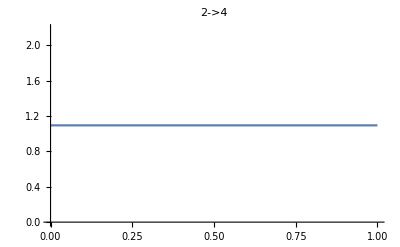

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-1.71828&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-0.0936949&&j16-j22-u40+u46==-1.18962

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-1.71828&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-0.0936949&&j16-j22-u40+u46==-1.18962

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-1.71828&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-0.0936949&&j16-j22-u40+u46==-1.18962

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-1.71828&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-0.0936949&&j16-j22-u40+u46==-1.18962

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

FRX1: nonlinear: 
j14-j20-u38+u44==-1.71828&&j15-j21-u39+u45==-1.71828&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.828625

<|j14→1,j15→0.140861,j16→0.859139,j17→0.140861,j18→0.859139,j19→1,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt28→0.140861,jt29→0.859139,jt30→0,jt31→0,jt32→0,jt33→0,jt34→0.140861,jt35→0,jt36→0.859139,jt37→0,u38→7.57742,u39→1.85914,u40→1.85914,u41→0,u42→1,u43→7.57742,u44→4.85914,u45→0.,u46→1.,u47→0,u48→1,u49→7.57742|>

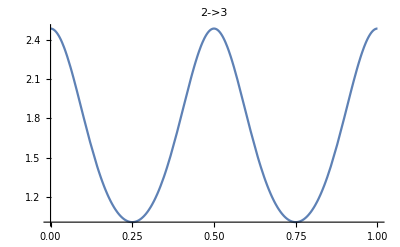
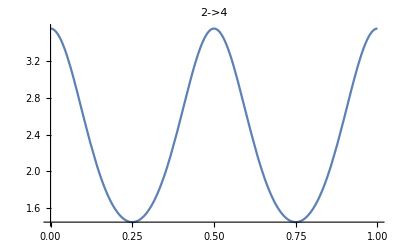
{-Graphics-,-Graphics-,-Graphics-}

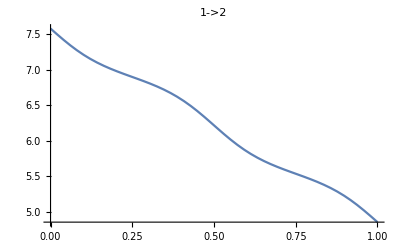
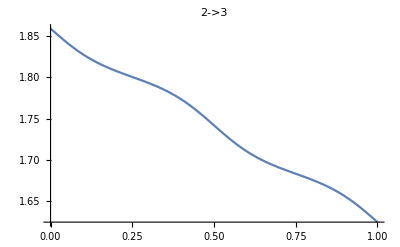
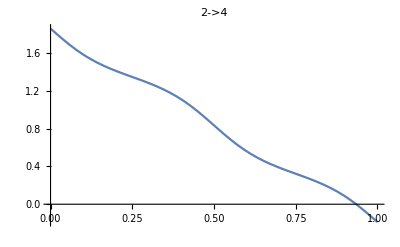

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],9,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.368074&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.115216

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.259739&&j16-j22-u40+u46==-0.0392193

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0436104

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.300245&&j16-j22-u40+u46==-0.0230616

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0171303

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.284239&&j16-j22-u40+u46==-0.0291655

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00662567

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.290417&&j16-j22-u40+u46==-0.0267708

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0025777

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.288012&&j16-j22-u40+u46==-0.0276972

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00100055

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.288945&&j16-j22-u40+u46==-0.0273368

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000388716

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.288582&&j16-j22-u40+u46==-0.0274767

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000150965

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.288723&&j16-j22-u40+u46==-0.0274223

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000586375

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.288668&&j16-j22-u40+u46==-0.0274435

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000227748

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.28869&&j16-j22-u40+u46==-0.0274353

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.84587×10^-6

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.288681&&j16-j22-u40+u46==-0.0274384

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.43577×10^-6

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.288685&&j16-j22-u40+u46==-0.0274372

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.33447×10^-6

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.288683&&j16-j22-u40+u46==-0.0274377

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.18314×10^-7

FRX1: nonlinear: 
j14-j20-u38+u44==-0.368074&&j15-j21-u39+u45==-0.288684&&j16-j22-u40+u46==-0.0274375

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.01316×10^-7

<|j14→1,j15→0.869377,j16→0.130623,j17→0.869377,j18→0.130623,j19→1,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt28→0.869377,jt29→0.130623,jt30→0,jt31→0,jt32→0,jt33→0,jt34→0.869377,jt35→0,jt36→0.130623,jt37→0,u38→5.52613,u39→1.15806,u40→1.15806,u41→0,u42→1,u43→5.52613,u44→4.15806,u45→2.22045×10^-16,u46→1.,u47→0,u48→1,u49→5.52613|>

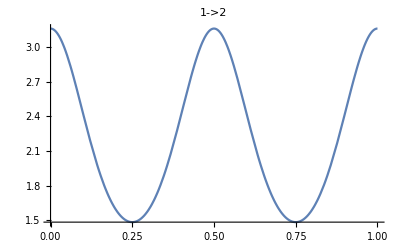
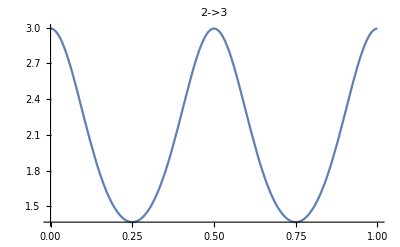
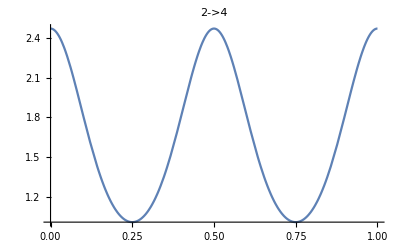

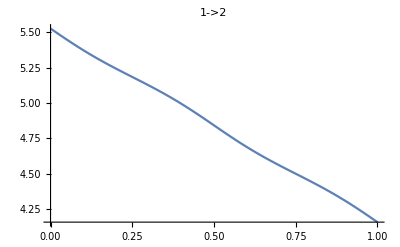
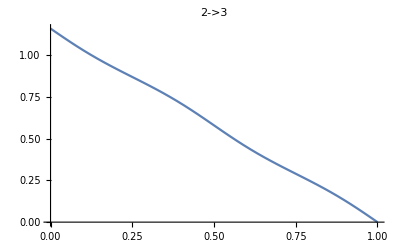
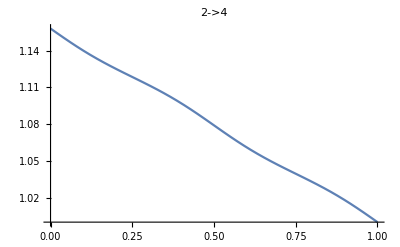

```mathematica
alpha = 1.4;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```

FRX1: nonlinear: 
j14-j20-u38+u44==0.0666076&&j15-j21-u39+u45==0.0666076&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.11022×10^-16

FRX1: nonlinear: 
j14-j20-u38+u44==0.0666076&&j15-j21-u39+u45==0.0666076&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.11022×10^-16

<|j14→1,j15→1.,j16→0.,j17→1.,j18→0.,j19→1,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt28→1.,jt29→0.,jt30→0,jt31→0,jt32→0,jt33→0,jt34→1.,jt35→0,jt36→0.,jt37→0,u38→4.86678,u39→0.933392,u40→0.933392,u41→0,u42→1,u43→4.86678,u44→3.93339,u45→0.,u46→0.933392,u47→0,u48→1,u49→4.86678|>

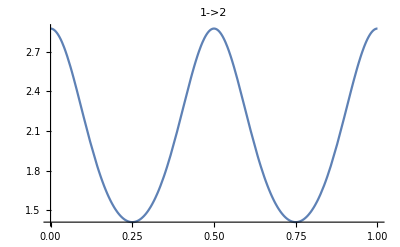
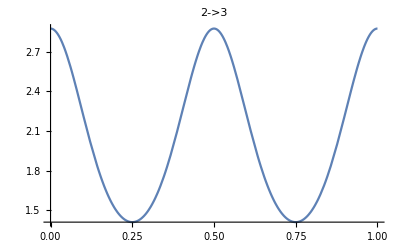
{-Graphics-,-Graphics-,-Graphics-}

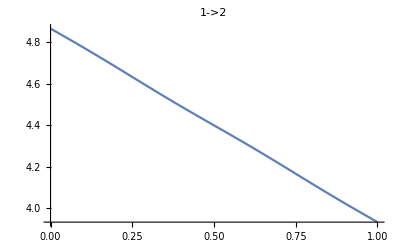
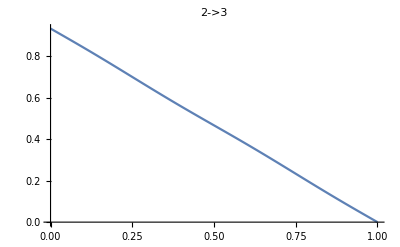
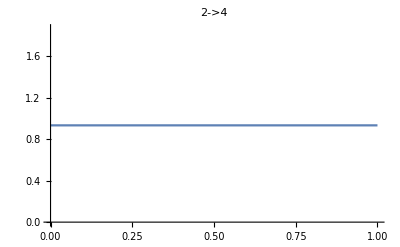

```mathematica
alpha = .9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```

FRX1: nonlinear: 
j14-j20-u38+u44==-0.0748868&&j15-j21-u39+u45==-0.0748868&&j16-j22-u40+u46==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00477913

FRX1: nonlinear: 
j14-j20-u38+u44==-0.0748868&&j15-j21-u39+u45==-0.0704377&&j16-j22-u40+u46==-0.00174516

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000390117

FRX1: nonlinear: 
j14-j20-u38+u44==-0.0748868&&j15-j21-u39+u45==-0.0708&&j16-j22-u40+u46==-0.00160053

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000319623

FRX1: nonlinear: 
j14-j20-u38+u44==-0.0748868&&j15-j21-u39+u45==-0.0707703&&j16-j22-u40+u46==-0.00161237

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.61784×10^-6

FRX1: nonlinear: 
j14-j20-u38+u44==-0.0748868&&j15-j21-u39+u45==-0.0707727&&j16-j22-u40+u46==-0.0016114

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.14418×10^-7

FRX1: nonlinear: 
j14-j20-u38+u44==-0.0748868&&j15-j21-u39+u45==-0.0707725&&j16-j22-u40+u46==-0.00161148

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.75621×10^-8

<|j14→1,j15→0.965419,j16→0.0345805,j17→0.965419,j18→0.0345805,j19→1,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt28→0.965419,jt29→0.0345805,jt30→0,jt31→0,jt32→0,jt33→0,jt34→0.965419,jt35→0,jt36→0.0345805,jt37→0,u38→5.11108,u39→1.03619,u40→1.03619,u41→0,u42→1,u43→5.11108,u44→4.03619,u45→-2.22045×10^-16,u46→1.,u47→0,u48→1,u49→5.11108|>

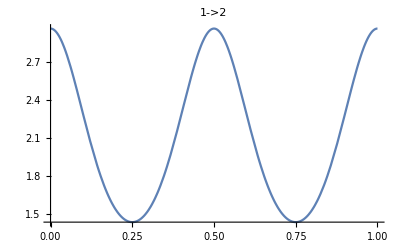
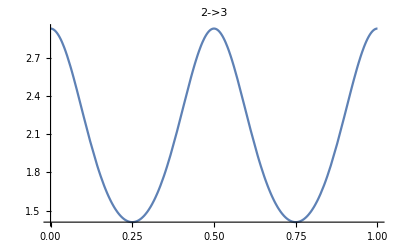
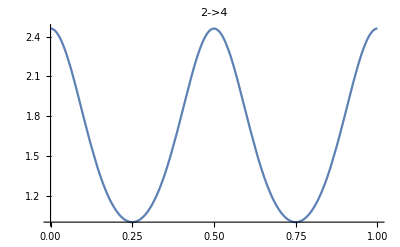

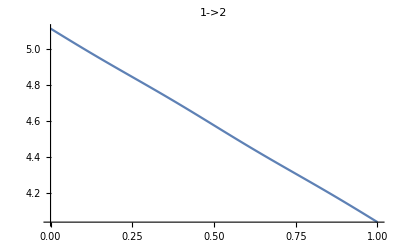
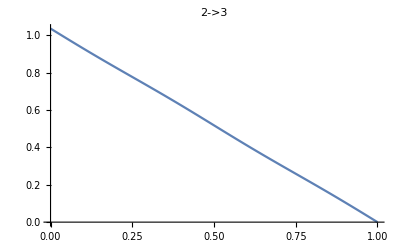
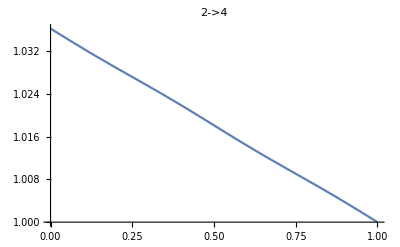

```mathematica
alpha = 1.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#]&/@MFGEquations["BEL"]
```

```mathematica
NIntegrate[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}]&/@MFGEquations["BEL"]
```

{2.12061,2.09097,1.64934}